Predicting Chemical Properties From Structure

Marc Thomson

Peter Barendse

University of Colorado at Boulder

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: This project predicts physical properties of organic compounds based on chemical structure. In particular, the code estimates melting point, boiling point, heat of fusion, heat of vaporization, heat of combustion, and heat of formation. These properties are determined from chemical structure and properties that can easily be calculated from structure. They do not require any experimental or quantum mechanical data as inputs.

SUMMARY OF WORK: Mathematica includes a large repository of chemical data that proves useful for this project, with around 44,000 entries. These data were filtered to remove missing entries, as well as those containing elements other than Carbon, Hydrogen, Nitrogen, and Oxygen, leaving around 5500 samples. Most of the work lay in processing the data and extracting useful features. Features included the molecule’s geometry, topology, functional groups and substructures, moments of inertia, as well as a host of other features. Once the data was gathered and saved, properties were predicted by the random forest algorithm, which performed better than neural networks.

RESULTS AND FUTURE  WORK: The machine learning algorithm predicted melting point with moderate accuracy. The MAE of the predictions was about 30 K, with an average relative error of 10%. Predictions of other properties fared much the same. It may be that accurate prediction from structure has a limit, and quantum mechanical information is required for accuracy. Future studies should include estimates of dipole moments, as well as a broader range of organic molecules (e.g., compounds containing Sulfur, Phosphorous, and halogens). Further improvements can be made by describing how molecules fit together in 3D space.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

All properties are in K:

Property | Standard Deviation | MAE | Median Error | Mean % Error
Melting Point | 41.4679 | 30.4487 | 23.337 | 9.95631
Boiling Point | 68.582 | 49.782 | 37.16 | 10.11

All properties are in KJ/Mol:

Property | Standard Deviation | MAE | Median Error
Heat of Fusion | 8.72 | 6.18 | 3.9
Heat of Vaporization | 21.83 | 7.22 | 3.29
Heat of Combustion | 1506.24 | 557.01 | 155.43
Heat of Formation | 779.79 | 312.74 | 85.04

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

### Feature Extraction

The key challenge of this project is figuring how to represent the structure of a molecules numerically. Ultimately, it was most effective to investigate different classes of features, as listed below.

#### Substructures/Functional Groups

Molecules be easily represented as graphs, where the vertices represent atoms and the edges represent bonds. Early on, machine learning was performed on the adjacency matrices of molecular graphs, but this was unable to successfully predict properties with any accuracy.

Instead, all unique subgraphs of the molecule were identified. Unique, in this context, means that the subgraph contains a different subset of connected non-hydrogen atoms, and all attached hydrogens. As an example, consider 2-Hydroxy-4-Methoxybenzoic Acid, pictured below.

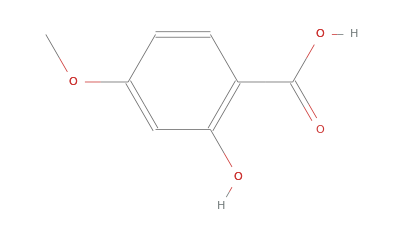

When analyzed by the method above, the following subgraphs are produced. Note that the scaling, orientation, and shape of these graphs are arbitrary; all that matters are the constituent atoms and bonds. If multiple graphs are identical, that means that the substructure appears more than once.

Some of these graphs correspond to traditional functional groups (ether, carboxylic acid, alcohol, carbonyl, etc). Many more of the groups seem arbitrary, but might hold information worth considering. Each graph is assigned a unique integer value, and stored as part of the dataset. Before prediction, the most common integers from the training set are taken to be features. The frequency of occurrence of each of these integers are input as a numerical vector.

#### Topological Features

In addition to enumeration of subgraphs, the topology of a molecular can be captured with various topological descriptors. These descriptors capture the connectivity and shape of the molecule. Some examples are the Weiner Index, Kier and Hall valence connectivity indices, and the Kier shape indices. More information about these descriptors can be found at CodessaPro’s website, as listed in the references.

#### Geometric Features

The geometry of a molecule determines how well it bonds to itself and influences its stability. To calculate the geometric features of a molecule, a mesh is generated with the atoms treated as spheres with van der Waals radii. Below is a mesh for 2-Hydroxy-4-Methoxybenzoic Acid. The surface area and volume of this can be easily calculated.

Because atoms stack in a condensed states, the minimum bounding box size might be important. Below is the bounding for for the same molecule. Features here include the lengths of the sides, the volume, and the surface area of the box.

Finally, the size of the convex hull of a molecule also plays a role in its properties. This is the mesh that would form if a molecule were wrapped in wrapping paper. The surface area and volume are recorded for this mesh.

#### Inertial Features

The principal moment of inertia of a molecules put it into one of three categories: spherical, oblate, or prolate. These classes give a rough idea of shape, so it is worth considering. Rather than attempt to classify shape, it is useful to input the moments as a vector. Below are the principal axes of inertia for 2-Hydroxy-4-Methoxybenzoic Acid.

#### Other Features

A number of miscellaneous features influence molecular properties: molar mass, number of rotatable bonds, and tallies of types of atoms and bonds. This and more information is included in the model as well.

#### Rejected Features

There were several features that I determined to be useless.

First, there is the SMILES string. Every chemical has a canonical string associated with it, that describes its properties. For example:

```mathematica
ChemicalData["Caffeine","SMILES"]
```

CN1C=NC2=C1C(=O)N(C(=O)N2C)C

Originally, I planned to use a RNN to predict properties using this string. However, I was unable to produce accurate results, so I will not include data from SMILES in my final model. Still, it is a path worth pursuing in the future.

There are also the atomic positions in ChemicalData[]. Though these are useful for calculating geometric properties, machine learning directly on the atomic positions was ineffective.

### Prediction

#### Melting Point

Most of the work in this project was directed to predict melting point, as this has historically been quite challenging. The difficulty in predicting melting point is easy to see. Take a set of molecules similar to benzene, for instance:

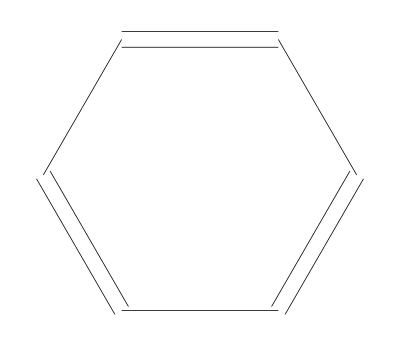
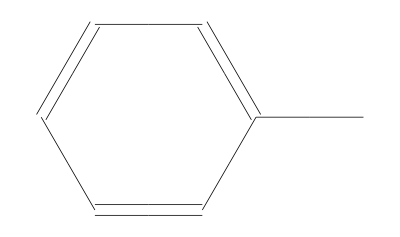
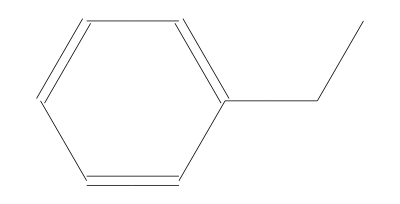
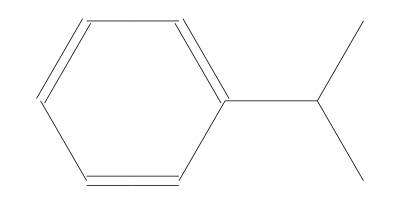
Benzene | -Graphics- | 278.65 K
Toluene | -Graphics- | 180.15 K
Ethylbenzene | -Graphics- | 178.15 K
Cumene | -Graphics- | 177.15 K

```mathematica
Grid[{#,ChemicalData[#,"BlackStructureDiagram"],UnitConvert[ChemicalData[#,"MeltingPoint"]]}&/@{"Benzene","Toluene","Ethylbenzene","Cumene"},Frame->All]
```

The results of this experiment show that melting point doesn’t behave linearly as groups are added. The first methyl group added drops the melting point by 100 K. The other two methyl groups, when added, do not change the melting point significantly.

To predict melting point, a random forest algorithm was employed, with 250 trees of leaf size 3. Below is a comparison plot of the results, with the tooltip containing the compound name. The closer the data are to the y=x line, the better the fit. Thus, the model predicts some aspects of the trend in melting point, but is unable to fully explain the variance.

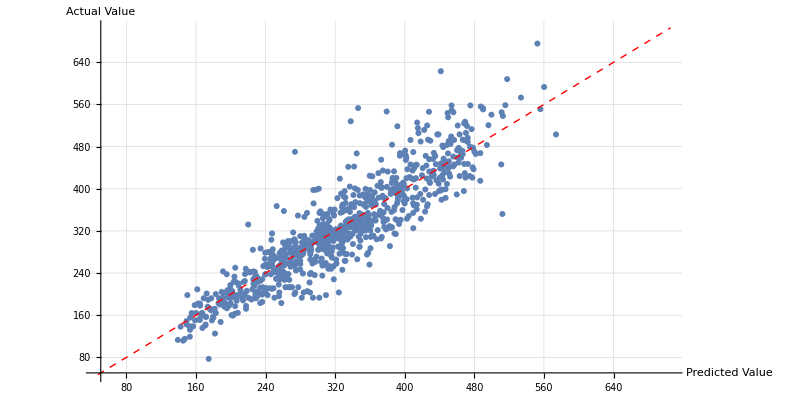

Below is a histogram of the residuals. For a good fit, the plot should look roughly normal. The normality here seems reasonable.

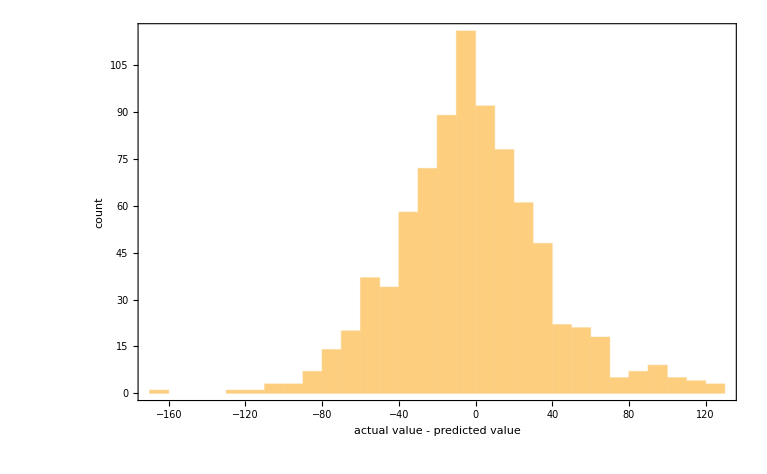

The important statistics are:

Standard Deviation of Residuals:		41.4679

Mean Absolute Value of Residuals:	30.4487

Median Absolute Value of Residuals:	23.337

Mean Percentage Error:			9.95631

Thus, this model can produce an approximate value for melting point, but cannot produce extremely accurate results. Still, such a model might be useful for screening purposes.

#### Boiling Point

Boiling point has historically been easier to predict, as it is less dependent on the exact shape of the molecule. To illustrate this, examine the same molecules as above.

```mathematica
Grid[{#,ChemicalData[#,"BlackStructureDiagram"],UnitConvert[ChemicalData[#,"BoilingPoint"]]}&/@{"Benzene","Toluene","Ethylbenzene","Cumene"},Frame->All]
```

Benzene | -Graphics- | 353.15 K
Toluene | -Graphics- | 383.65 K
Ethylbenzene | -Graphics- | 409.15 K
Cumene | -Graphics- | 426.15 K

Unlike the previous case, the boiling point increases regularly as the molecule grows larger.

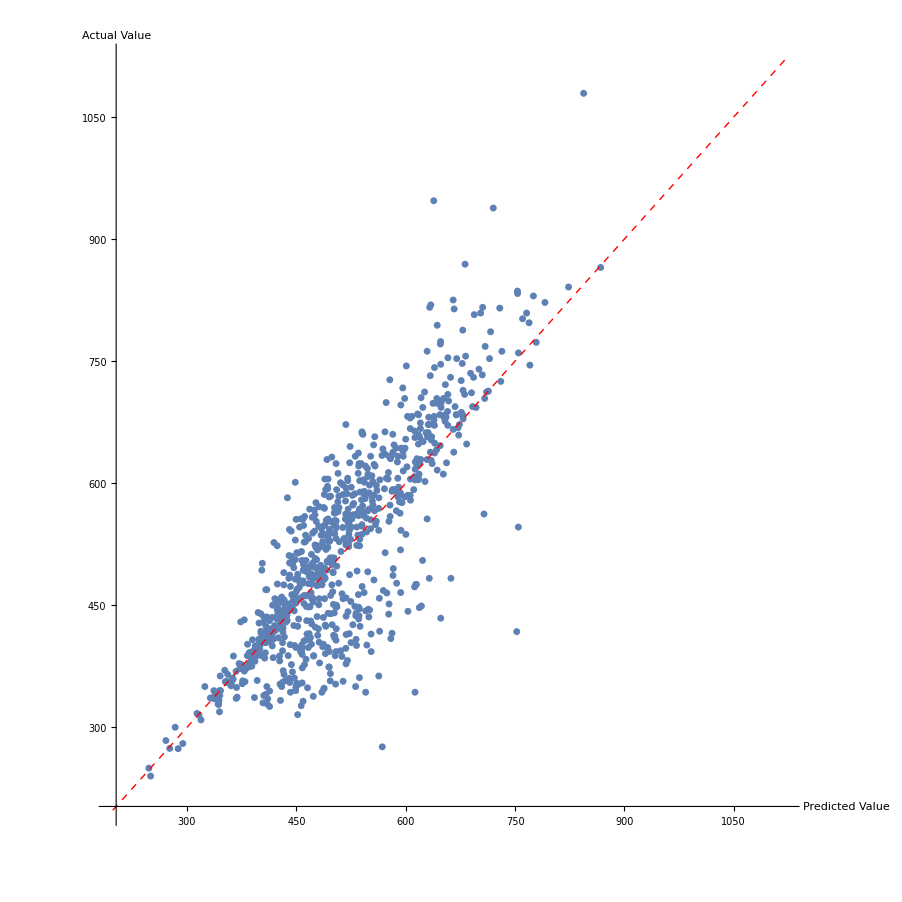
Random forest was also applied to predict boiling point. Below is the resulting comparison plot. Clearly, it is not as easy to predict boiling point as hypothesized above. Examining the plot closely reveals that the data are not distributed evenly about the y=x line: there seems to be a large group of chemicals whose boiling points are over-predicted. It is likely that there is yet another feature not taken into account by this model’s feature extraction. More research into the literature might find what is missing, and this could be applied to the other properties in this list.
 
-Graphics-

The residual histogram, which should appear normal, appears quite asymmetric.

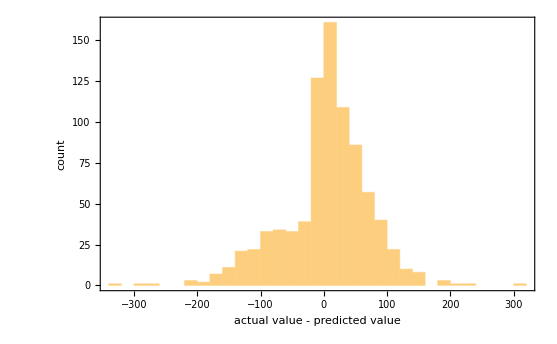

The important statistics are:

Standard Deviation of Residuals:		68.582

Mean Absolute Value of Residuals:	49.782

Median Absolute Value of Residuals:	37.16

Mean Percentage Error:			10.11

This method was largely unsuccessful at predicting boiling point, indicating that there are more features to discover.

#### Heat of Fusion

A detailed literature search for the factors that influence heat of fusion was not done, so it is unclear how well this prediction will work. Presumably, it is dependent on similar properties as melting point, such as how well molecules bond to each other. Once again, take a set of molecules related to benzene:

```mathematica
Grid[{#,ChemicalData[#,"BlackStructureDiagram"],UnitConvert[ChemicalData[#,"MeltingPoint"]],UnitConvert[ChemicalData[#,"FusionHeat"]]}&/@{"Benzene","Toluene","Ethylbenzene","Cumene"},Frame->All]
```

Benzene | -Graphics- | 278.65 K | 9870. kg m^2/(s^2 mol)
Toluene | -Graphics- | 180.15 K | 6640. kg m^2/(s^2 mol)
Ethylbenzene | -Graphics- | 178.15 K | 9180. kg m^2/(s^2 mol)
Cumene | -Graphics- | 177.15 K | 7330. kg m^2/(s^2 mol)

This is only anecdotal evidence, so it is useful to view the correlation over all compounds. The plot of melting point versus enthalpy of fusion is displayed below, showing a general, albeit weak, correlation.

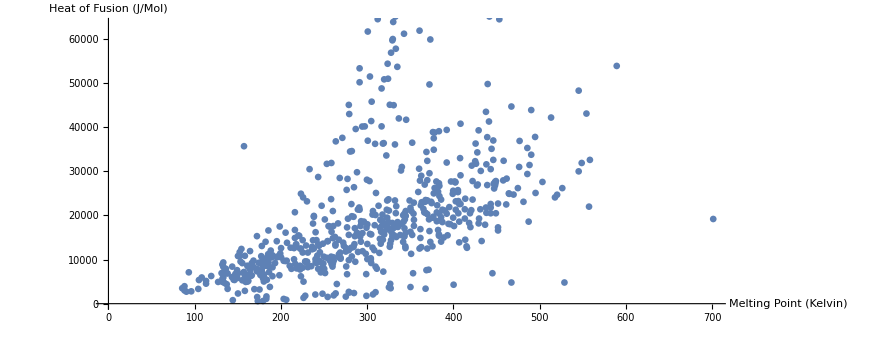

Using a similar prediction algorithm as above, the following comparison plot is produced. Because few compounds have heat of fusions measured, the sample size is smaller. Much like melting point predictions, there is a clear correlation, but the model does not fully explain the observations.

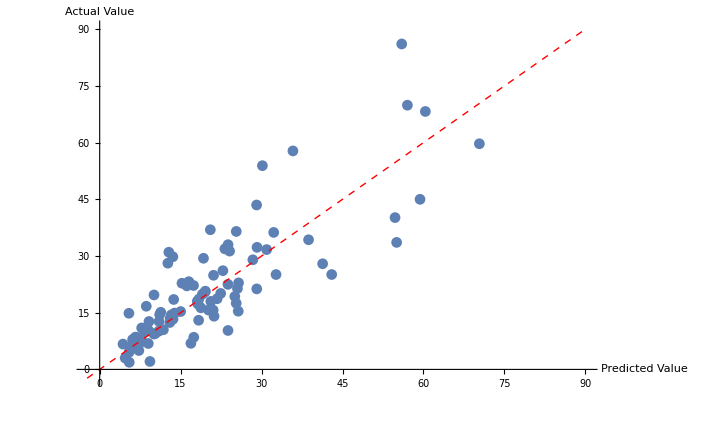

The model is fairly normal, though appears to have some degree of skew. It is possible that increasing the sample size would remove skew.

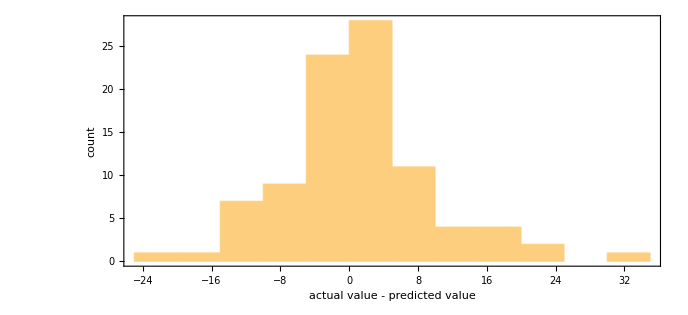

The important statistics are:

Standard Deviation of Residuals:		8.72

Mean Absolute Value of Residuals:	6.18

Median Absolute Value of Residuals:	3.90

Thus, this model is able to approximate enthalpies of fusion, but not fully predict them.

#### Heat of Vaporization

Much like heat of fusion, there seemingly should be a strong correlation between boiling point and heat of vaporization. Examining the benzene-like molecules:

```mathematica
Grid[{#,ChemicalData[#,"BlackStructureDiagram"],UnitConvert[ChemicalData[#,"BoilingPoint"]],UnitConvert[ChemicalData[#,"VaporizationHeat"]]}&/@{"Benzene","Toluene","Ethylbenzene","Cumene"},Frame->All]
```

Benzene | -Graphics- | 353.15 K | 33830. kg m^2/(s^2 mol)
Toluene | -Graphics- | 383.65 K | 38010. kg m^2/(s^2 mol)
Ethylbenzene | -Graphics- | 409.15 K | 42300. kg m^2/(s^2 mol)
Cumene | -Graphics- | 426.15 K | 45100. kg m^2/(s^2 mol)

There appears to be a decent correlation between boiling point and heat of vaporization. This implies that the missing features that prevented accurate modeling of boiling point might also prevent accurate modelling of vaporization enthalpy. Generalized Trouton’s rule models this correlation, and is plotted below in red along with a host of relevant compounds. Trouton’s rule seems to model most of the data fairly well, aside from a large chunk of data at the top left. This is likely the same data whose boiling points were much lower than predicted. It is possible that these compounds have some features that cause this outlying behavior, or it is possible that the measured boiling points are incorrect. Alternatively, the data points that follow trends very similar to Trouton’s rule might be predicted, not experimental, data.

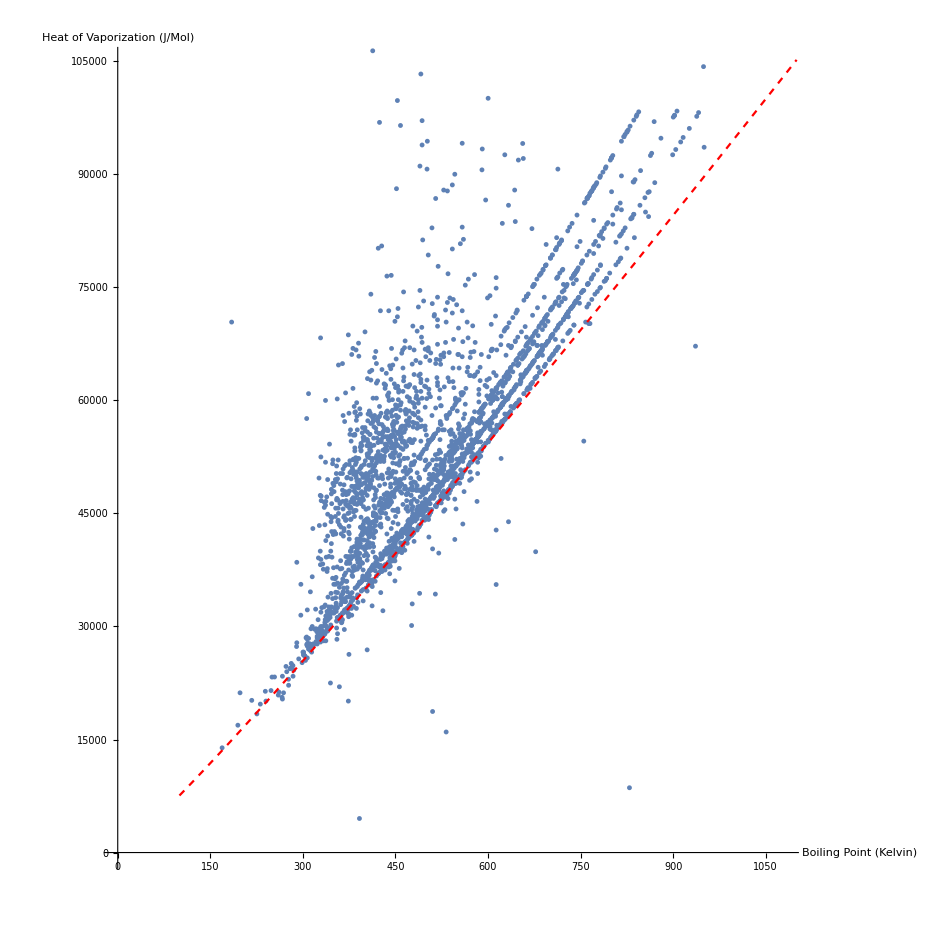

Prediction is done using a random forest model. The comparison plot is below. The data is immediately marked by a very prominent outlier, N-methyl pyrrole, with an actual heat of vaporization of 407 KJ/mol. This seems to be incorrect data, as NIST lists the heat of vaporization as 40.7 KJ/mol (see sources.) Aside from this outlier, the data is fairly well correlated, but as in the previous cases, the model is insufficient to fully predict heat of vaporization.

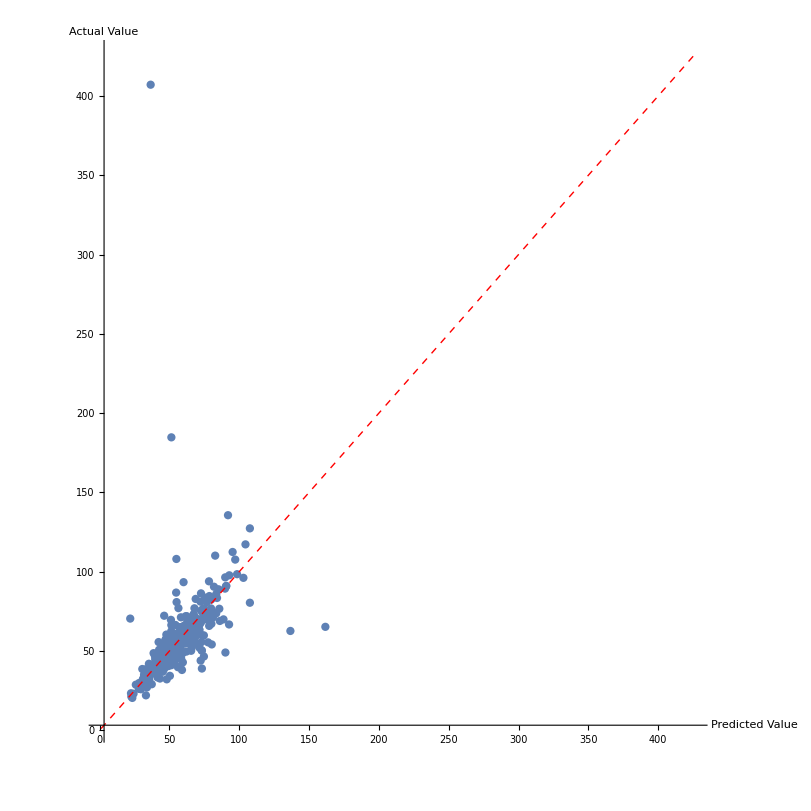

The plot of residuals appears fairly normal, though has very prominent tails. This might be caused by the reduced sample size

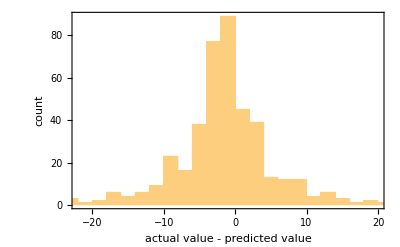

The important statistics are (measured in KJ/mol):

Standard Deviation of Residuals:		21.831

Mean Absolute Value of Residuals:	7.224

Median Absolute Value of Residuals:	3.288

The mean absolute error is actually fairly small, allowing for moderately accurate prediction.

#### Heat of Combustion

Heat of combustion is relatively easy to predict. It is closely correlated with the number of bonds of different types. Conjugation, as in aromatic rings, can lower a molecule’s energy, thus reducing its heat of combustion. Precise predication will require a more detailed model, such as the one presented here. To begin, evaluate the benzene-family molecules.

```mathematica
Grid[{#,ChemicalData[#,"BlackStructureDiagram"],UnitConvert[ChemicalData[#,"CombustionHeat"]]}&/@{"Benzene","Toluene","Ethylbenzene","Cumene"},Frame->All]
```

Benzene | -Graphics- | 3.275×10^6 kg m^2/(s^2 mol)
Toluene | -Graphics- | 3.9103×10^6 kg m^2/(s^2 mol)
Ethylbenzene | -Graphics- | 4.568×10^6 kg m^2/(s^2 mol)
Cumene | -Graphics- | 4.513×10^6 kg m^2/(s^2 mol)

As expected, heat of combustion correlates fairly closely with size. The comparison plot resulting from the random forest algorithm shows fairly strong prediction, with a few significant outliers. Generally however, data points are very close to the perfect prediction line.

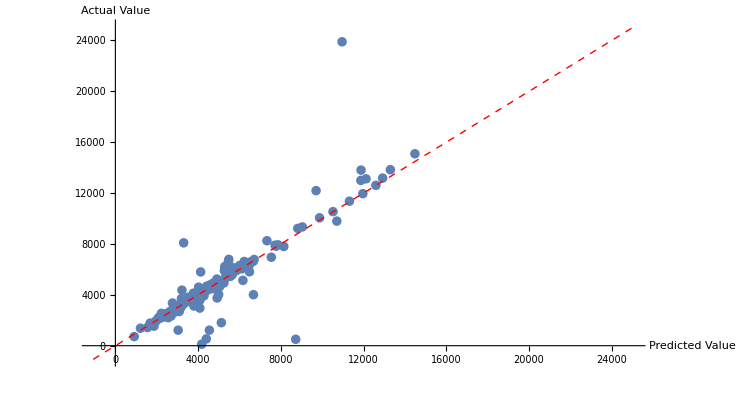

The residuals appear moderately normally distributed, with fairly strong tails.

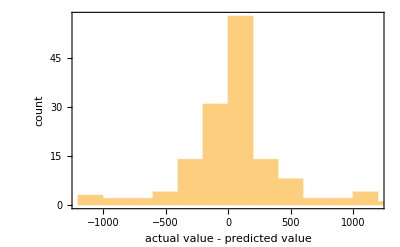

The important statistics are:

Standard Deviation of Residuals:		1506.24

Mean Absolute Value of Residuals:	557.01

Median Absolute Value of Residuals:	155.43

The standard deviation and mean residuals are significant skewed by the outliers, but the values are not terrible high. Even a difference of 500 KJ/mol is not too far off for combustion. Generally, this model performs adequately. It might benefit from a larger sample size.

#### Heat of Formation

Heat of formation is more or less the same as heat of formation, but it is worth investigating if altering the form of the data changes how well the model does. The enthalpy of formation is not directly available in ChemicalData[], but can be calculated from Hess’s Law. For this prediction, compounds containing nitrogen must be removed, because combustion thereof produces an uncertain mixture of nitric oxides. For compounds of C,H, and O, combustion produces predictable quantities of water and carbon dioxide.

Running a random forest on this produces the following comparison plot. It is marked by significant outliers, but a general correlation.

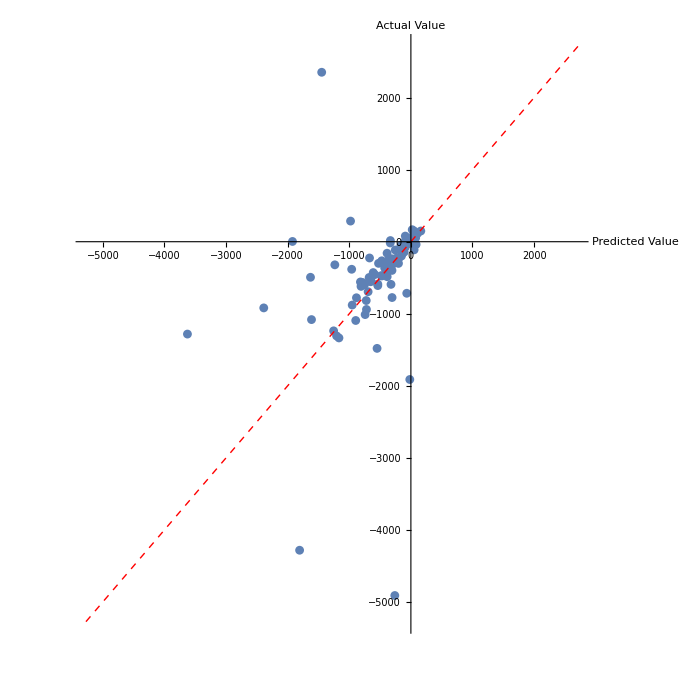

The data are fairly normal, but have strong tails due to the outliers.

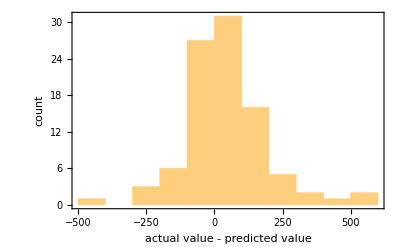

The important statistics are:

Standard Deviation of Residuals:		779.79

Mean Absolute Value of Residuals:	312.74

Median Absolute Value of Residuals:	85.04

For most molecules, this model is able to closely model its enthalpy of formation, with a mean deviation of 300. Thus, this model can roughly predict enthalpy of formation.

Code

The code is available below. To perform this analysis, the user must preprocess data, which can take upwards of 24 hours. This is done in FinalProjectPreprocess.m. Actual prediction of properties takes place FinalProjectPredict.m, which uses the .wl file created by the preprocessing. Both files are fairly long, so the code is not copied here.

https://github.com/MarcThomson/WSS2017_Project

An example of the input can be found below. This requires the dataset being in the current directory.

#### Example Input

```mathematica
fileLoc=NotebookDirectory[];
nFeat=250;
tempfile=StringJoin[fileLoc,"FinalSet.wl"];
Get[tempfile];
totalSet=RandomSample[totalSet,Length[totalSet]];

Lset=Length[totalSet];

trainSet=totalSet[[1;;Round[0.7*Lset]]];
testSet=totalSet[[Round[0.7*Lset]+1;;Round[0.85*Lset]]];
validSet=totalSet[[Round[0.85*Lset]+1;;]];

hashesTrain=Table[trainSet[[i]]["Hashes"],{i,1,Length[trainSet]}];
hashesTest=Table[testSet[[i]]["Hashes"],{i,1,Length[testSet]}];
hashesValid=Table[validSet[[i]]["Hashes"],{i,1,Length[validSet]}];

flatHashes=Flatten[DeleteDuplicates/@hashesTrain];
commonHashes=SortBy[Tally[flatHashes],-#[[2]]&];

(*featureList=#[[2]]&/@Select[commonHashes,#[[2]]>100&];*)
featureList=Commonest[flatHashes,nFeat];

groupsTrain=Table[Count[hashesTrain[[i]],featureList[[j]]],{i,1,Length[hashesTrain]},{j,1,Length[featureList]}];
groupsTest=Table[Count[hashesTest[[i]],featureList[[j]]],{i,1,Length[hashesTest]},{j,1,Length[featureList]}];
groupsValid=Table[Count[hashesValid[[i]],featureList[[j]]],{i,1,Length[hashesValid]},{j,1,Length[featureList]}];

atomTalliesTrain=Table[trainSet[[i]]["AtomTally"],{i,1,Length[trainSet]}];
atomTalliesTest=Table[testSet[[i]]["AtomTally"],{i,1,Length[testSet]}];
atomTalliesValid=Table[validSet[[i]]["AtomTally"],{i,1,Length[validSet]}];

allInputsTrain=Table[
				Flatten[
					{groupsTrain[[i]],
					trainSet[[i]]["Cis"],
					trainSet[[i]]["Trans"],
					trainSet[[i]]["BondTally"],
					trainSet[[i]]["TopoFeatures"],
					trainSet[[i]]["Geom"],
					Total[Abs[trainSet[[i]]["FormalCharges"]]],
					QuantityMagnitude[trainSet[[i]]["TopologicalPolarSurfaceArea"]],
					trainSet[[i]]["NetCharge"],
					trainSet[[i]]["RotatableBondCount"],
					trainSet[[i]]["HBondAcceptorCount"],
					trainSet[[i]]["HBondDonorCount"],
					trainSet[[i]]["PrincipalMom"],
					QuantityMagnitude[trainSet[[i]]["MolarMass"]],
					QuantityMagnitude[trainSet[[i]]["MolarMass"]]/Total[atomTalliesTrain[[i]]],
					atomTalliesTrain[[i]]}
				],
				{i,1,Length[trainSet]}];

allInputsTest=Table[
				Flatten[
					{groupsTest[[i]],
					testSet[[i]]["Cis"],
					testSet[[i]]["Trans"],
					testSet[[i]]["BondTally"],
					testSet[[i]]["TopoFeatures"],
					testSet[[i]]["Geom"],
					Total[Abs[testSet[[i]]["FormalCharges"]]],
					QuantityMagnitude[testSet[[i]]["TopologicalPolarSurfaceArea"]],
					testSet[[i]]["NetCharge"],
					testSet[[i]]["RotatableBondCount"],
					testSet[[i]]["HBondAcceptorCount"],
					testSet[[i]]["HBondDonorCount"],
					testSet[[i]]["PrincipalMom"],
					QuantityMagnitude[testSet[[i]]["MolarMass"]],
					QuantityMagnitude[testSet[[i]]["MolarMass"]]/Total[atomTalliesTest[[i]]],
					atomTalliesTest[[i]]}
					],
					{i,1,Length[testSet]}];
					
allInputsValid=Table[
				Flatten[
					{groupsValid[[i]],
					validSet[[i]]["Cis"],
					validSet[[i]]["Trans"],
					validSet[[i]]["BondTally"],
					validSet[[i]]["TopoFeatures"],
					validSet[[i]]["Geom"],
					Total[Abs[validSet[[i]]["FormalCharges"]]],
					QuantityMagnitude[validSet[[i]]["TopologicalPolarSurfaceArea"]],
					validSet[[i]]["NetCharge"],
					validSet[[i]]["RotatableBondCount"],
					validSet[[i]]["HBondAcceptorCount"],
					validSet[[i]]["HBondDonorCount"],
					validSet[[i]]["PrincipalMom"],
					QuantityMagnitude[validSet[[i]]["MolarMass"]],
					QuantityMagnitude[validSet[[i]]["MolarMass"]]/Total[atomTalliesValid[[i]]],
					atomTalliesValid[[i]]}
					],
					{i,1,Length[validSet]}];


outputTrain=Table[
				QuantityMagnitude[
					UnitConvert[
						trainSet[[i]]["MeltingPoint"],
						"Kelvins"
						]
					],
				{i,1,Length[trainSet]}];

outputTest=Table[
				QuantityMagnitude[
					UnitConvert[
						testSet[[i]]["MeltingPoint"],
						"Kelvins"
						]
					],
				{i,1,Length[testSet]}];
				
outputValid=Table[
				QuantityMagnitude[
					UnitConvert[
						validSet[[i]]["MeltingPoint"],
						"Kelvins"
						]
					],
				{i,1,Length[validSet]}];
				
					
							

trainData=Thread[allInputsTrain-> outputTrain];
testData=Thread[allInputsTest-> outputTest];
validData=Thread[allInputsValid-> outputValid];

p=Predict[trainData,ValidationSet->validData,FeatureTypes->"NumericalVector",PerformanceGoal->"Quality",Method->{"RandomForest","TreeNumber"-> 250,"LeafSize"->3}];
```

Written Content / Lesson Plans

Conclusions in Detail

The model employed the random forest algorithm, which was found to be more accurate than neural networks. Melting point was predicted with a mean average error of 30 K, which is larger than the results of Lazzus, who used quantum mechanical data. This error is slightly lower than that found by Karthikeyan & Glen, who calculated a MAE of 37.6 K. The model performed more poorly on boiling point, with a mean average error of 50K. It appears as though there is another feature influencing boiling point that is unaccounted for in the feature extraction method. The model was able to approximately determine heats of formation and vaporization, with mean errors of 6.18 KJ/mol and 7.22 KJ/mol respectively. The prediction of vaporization enthalpy could be improved by taking into account the feature influencing boiling point. Heats of combustion and formation were each computed approximately, with MAE of 557 and 313 KJ/mol respectively. These errors are much larger in magnitude than those for fusion and vaporization, but are small relative the to the range of values for these properties. Unfortunately, percentage error cannot be calculated for the energetic predictions because any true values close to 0 would lead to near-infinite error.

Generally, it seems possible to approximate chemical properties of organic molecules from structure alone. Incorporation of quantum mechanical data or experimental data might increase accuracy, but would limit the usefulness of the model. Quantum mechanical data is computationally expensive and experiments can be time consuming. Instead, all inputs for this model can be found from simple local calculations. This input form allows for fast approximation of the properties of many molecules at once.

All Visualizations

Visualizations can be found interspersed with the results.

Data Sources Links/References

Wolfram Research, Inc., Wolfram|Alpha Knowledgebase, Champaign, IL (2017).

“NIST Chemistry WebBook, SRD 69.” 1-Methylpyrrole. National Institute of Standards and Technology, n.d. Web. 05 July 2017. <http://webbook.nist.gov/cgi/cbook.cgi?ID=C96548&Mask=4>.

"Molar Enthalpy of Formation of Various Substances." Ohio University, n.d. Web. 04 July 2017. <http://www.ohio.edu/mechanical/thermo/property_tables/combustion/Enth_Formation.html>.

Winter, Mark. “The Periodic Table of the Elements.” The Periodic Table of the Elements by WebElements. N.p., n.d. Web. 04 July 2017. <https://www.webelements.com/>.

Future Directions

Due to the limited timescale of this project, a great many options remain unexplored, many of which might improve its accuracy. The first area to improve is feature extraction. The failure of boiling point predictions, along with the general inaccuracy of other predictions, indicate that there are additional features that must be considered. The easiest way to begin is to look at the properties of molecules that are predicted poorly, and try to find some commonalities. A cursory glance was unable to identify a trend, but a more detailed study might reveal new features to be taken into account.

	One neglected feature is conjugation, the delocalization of atomic orbitals in certain configurations. This has enormous consequences for molecular properties. The model presented here requires that every bond is of integer order, when conjugated systems have fractional bond degrees. This discrepancy might cause enormous error. It is also important to find some new descriptors for 3D shape that might help with the problem of fitting molecules together in space. Rotatable bonds are an important consideration for this purpose; molecules can change conformation to better fit together. Stereochemistry is another shortcoming. To gain more information about stereochemistry, it will likely be required to get additional data outside of ChemicalData[]. Finally, though dipole moments cannot be accurately calculated without quantum mechanics, first order approximations are possible, such as with Gasteiger Charges.

Feature selection can also be implemented into the model. Currently, there is not any test of the statistical significance of the parameters. This is an issue particularly for the subgraphs. The model works by taking the subgraphs that appear in the most molecules, but these are not necessarily the most significant subgraphs. A comparison of significance could focus on the structures that add to the model. This would also help in selecting the number of structures to consider in the model. The number of unique structures is upwards of 10000, so it is necessary to choose a subset. The model currently takes the most common 250, but there is little evidence to back up this practice.

	The random forest algorithm was not significantly tuned to get the best output for each property. The algorithm ended up being very slow to converge, sometimes taking an entire night. Thus, it was difficult to figure out the precise hyperparameters to give the best results. Neural networks, both within and Predict[] and NetTrain[] were not able to beat the results of the random forest. It is possible that a properly constructed neural network, or a different machine learning algorithm, might be able to better predict chemical properties. This tuning could also be used to reduce overfitting. Though not mentioned above, the models were fairly overfit, producing much better results on the training set than the test set. 

	This model was constructed with blind trust for the data in ChemicalData[], but it would be worthwhile to spend time validating this data with alternate sources. This should have been done before beginning preprocessing, but was not due to time constraints. In the prediction steps, several incorrect data points were noticed, as well as some data points that may be a results of prediction instead of experiment. A closer look should be given to these cases to verify the data.
	
	Aside from accuracy, the model could be improved by broadening its scope. Including compounds containing sulfur, phosphorous, and halogens would cover most of organic chemistry. Due to time constraints, I was unable to download and process this larger data set, so I am unsure how well it would perform in comparison.

	Finally, if the recommendations are taken into account but still fail to produce an accurate model, it might not be possible to have a one-size-fits all model for organic properties. Instead, it might be more effective to classify molecules and model them separately. This would allow for more relevant features for each class of molecules.

Background Info Links/References

Karthikeyan, M., Robert C. Glen, and Andreas Bender. “General Melting Point Prediction Based on a Diverse Compound Data Set and Artificial Neural Networks.” Journal of Chemical Information and Modeling, vol. 45, no. 3, 2005, pp. 581-590.

"Theory: QSAR+ Descriptors." Accelrys, n.d. Web. 04 July 2017. <http://www.ifm.liu.se/compchem/msi/doc/life/cerius46/qsar/theory_descriptors.html>.

Katritzky, Alan, Mati Karelson, and Ruslan Petrukhin. "CODESSA PRO Classes of Descriptors." CODESSA PRO. N.p., n.d. Web. <http://www.codessa-pro.com/descriptors/index.htm>.

Lazzús, Juan A."Neural Network Based on Quantum Chemistry for Predicting Melting Point of Organic Compounds." Chinese Journal of Chemical Physics, vol.22, no.1, 2009, pp.19 - 26.

Rogers, David, and Mathew Hahn. "Extended-Connectivity Fingerprints." Journal of Chemical Information and Modeling, vol. 50, no. 5, 2010, pp. 742.

Libretexts. “Trouton’s Rule.” Chemistry LibreTexts. Libretexts, 09 Apr. 2017. Web. 05 July 2017. <https://chem.libretexts.org/Core/Physical_and_Theoretical_Chemistry/Thermodynamics/Introduction_to_Thermodynamics/Trouton’s_rule>.

Other thank you’s:

Peter Barendse

Mark Boyer

Bob Nachbar

Keywords

Provide keywords as items

Chemistry

Machine Learning

Chemicals

Organic Chemistry

Melting Point

Boiling Point

QSPR

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```